```mathematica
ClearAll["Global`*"]
```

```mathematica
p1=7467;e1=0.1;p2=7670;e2=0.10;d=2500000;a1=2;a2=1;(*p1=a1*(1-e1^2);p2=a2*(1-e2^2);*)
```

```mathematica
nudot[nu_,p_,e_] =Sqrt[1.0/p^3]*(1+e*Cos[nu])^2;
```

```mathematica
nux[nu_,p_,e_]=p/(1+e*Cos[nu])*Cos[nu];
```

```mathematica
nuy[nu_,p_,e_]=p/(1+e*Cos[nu])*Sin[nu];
```

```mathematica
distnu[nu1_,p1_,e1_,nu2_,p2_,e2_]=(nux[nu1,p1,e1]-nux[nu2,p2,e2])^2+(nuy[nu1,p1,e1]-nuy[nu2,p2,e2])^2;
```

```mathematica
(*flow=VectorPlot[{nudot[nu1,a1*(1-e1),e1],nudot[nu2,a2*(1-e2),e2]},{nu1,0,120},{nu2,0,360},VectorPoints->Fine,VectorScale->Tiny];*)
flow=StreamPlot[{nudot[nu1,p1,e1],nudot[nu2,p2,e2]},{nu1,0,2*Pi},{nu2,0,2*Pi}];
```

```mathematica
rend=RegionPlot[Evaluate[distnu[nu1,p1,e1,nu2,p2,e2]<=d],{nu1,0,2*Pi},{nu2,0,2*Pi}];
```

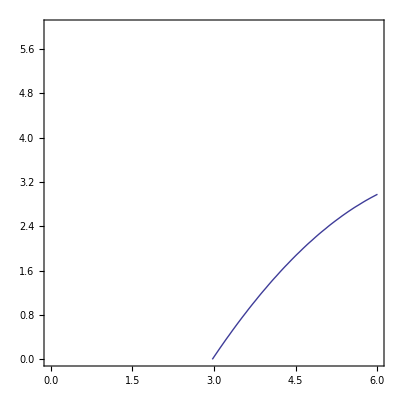

```mathematica
bc=ContourPlot[-5.768759376887889+2.418415469924801 nu1-0.16013695640259024 nu1^2-nu2==0,{nu1,0,6},{nu2,0,6}]
```

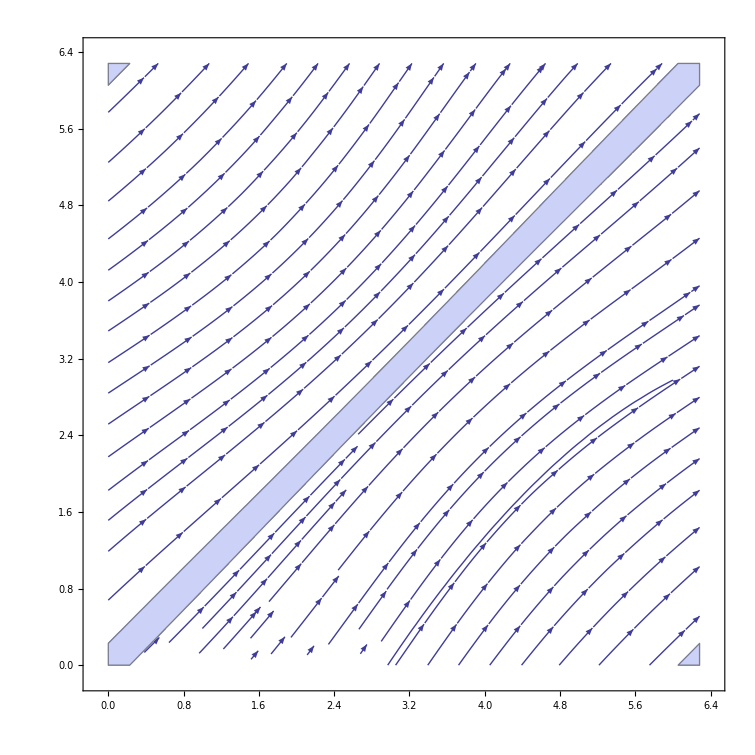

```mathematica
Show[flow,rend,bc]
```

```mathematica
Plot3D[(-7748*Sin[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Sin[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]-0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]^2-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]^2)+(-7748*Cos[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Cos[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(-0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]),{NU1,200,250},{NU2,100,13
0}]
```

-Graphics3D-

```mathematica
FullSimplify[(-7748*Sin[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Sin[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]-0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]^2-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]^2)+(-7748*Cos[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Cos[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(-0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2])]
```

((2.54711-1.20931 Cos[0.0174444 NU2]) Sin[0.0174444 NU2])/(200.5+30. Cos[0.0174444 NU2]+0.5 Cos[0.0348889 NU2])

```mathematica
%//FortranForm
```

((2.547109594446804 - 1.209310193209165*Cos(0.0174444444444444*NU2))*Sin(0.0174444444444444*NU2))/
     -  (200.5 + 30.*Cos(0.0174444444444444*NU2) + 0.5*Cos(0.0348888888888888*NU2))

```mathematica
Chop[Simplify[Expand[(-7748*Sin[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Sin[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2+(-7748*Cos[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Cos[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2-2500000]]]
```

-2500000+(2.00166×10^10)/(20.+1. Cos[0.0175 NU1])^2+(6.00315×10^9)/(10.+1. Cos[0.0175 NU2])^2-(2.19237×10^10 Cos[0.0175 NU1] Cos[0.0175 NU2])/((20.+1. Cos[0.0175 NU1]) (10.+1. Cos[0.0175 NU2]))-(2.19237×10^10 Sin[0.0175 NU1] Sin[0.0175 NU2])/((20.+1. Cos[0.0175 NU1]) (10.+1. Cos[0.0175 NU2]))

```mathematica
data=Table[{{nu1,nu2},{nudot[nu1,p1,e1],nudot[nu2,p2,e2]}},{nu1,0,6,0.01},{nu2,0,6,0.01}];
```

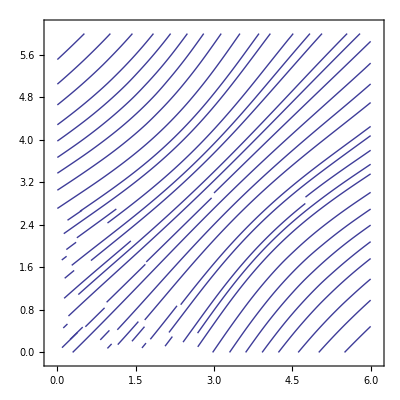

```mathematica
plot=ListStreamPlot[data,StreamStyle->"Line",PlotRangePadding->0]
```

```mathematica
points=plot[[1,2,1]];
```

```mathematica
indexes=Cases[plot,Line[index_]->index,Infinity];
```

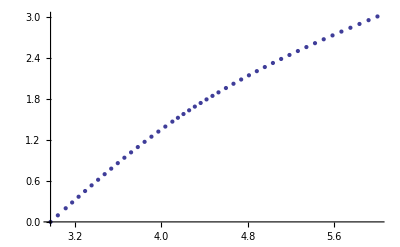

-5.76879+2.41843 x-0.160139 x^2

```mathematica
p=points[[indexes[[4]]]];
ListPlot[p]
Fit[p,{1,x,x^2},x]
```

```mathematica
Chop[FullSimplify[(-7748*Sin[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Sin[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))*(0.000416136218753746*(0.05*Cos[0.0175*NU1]+1)*Cos[0.0175*NU1]-0.000397624593682648*(0.1*Cos[0.0175*NU2]+1)*Cos[0.0175*NU2]+2.08068109376873*10^-5*Sin[0.0175*NU1]^2-3.97624593682648*10^-5*Sin[0.0175*NU2]^2)+(-7748*Cos[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Cos[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))*(-0.000416136218753746*(0.05*Cos[0.0175*NU1]+1)*Sin[0.0175*NU1]+0.000397624593682648*(0.1*Cos[0.0175*NU2]+1)*Sin[0.0175*NU2]+2.08068109376873*10^-5*Sin[0.0175*NU1]*Cos[0.0175*NU1]-3.97624593682648*10^-5*Sin[0.0175*NU2]*Cos[0.0175*NU2])]]
```

(-54.9464 Sin[0.0175 NU1]-28.128 Sin[0.0175 NU1-0.035 NU2]+80.2101 Sin[0.0175 NU1-0.0175 NU2]+16.1211 Sin[0.035 NU1-0.0175 NU2]-0.606581 Sin[0.0175 NU1+0.0175 NU2]+13.2526 Sin[0.0175 NU2])/((20.+1. Cos[0.0175 NU1]) (10.+1. Cos[0.0175 NU2]))

```mathematica
Plot3D[%342,{NU1,250,300},{NU2,50,360}]
```

Out::intm: Machine-sized integer expected at position 1 in Out[342.].

General::stop: Further output of Out :: intm will be suppressed during this calculation.

-Graphics3D-

```mathematica
%//CForm;
```

```mathematica
Chop[FullSimplify[(-7748*Sin[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Sin[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2+(-7748*Cos[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Cos[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2-250000]]
```

-250000+(64000.+1/(-7.06814×10^-6-3.53407×10^-7 Cos[0.0175 NU1])+1/(0.0000129066+1.29066×10^-6 Cos[0.0175 NU2]))^2+((141480. Sin[0.0175 NU1])/(20.+1. Cos[0.0175 NU1])-(77480. Sin[0.0175 NU2])/(10.+1. Cos[0.0175 NU2]))^2

```mathematica
D[%]
```

-250000+(64000.+1/(-7.06814×10^-6-3.53407×10^-7 Cos[0.0175 NU1])+1/(0.0000129066+1.29066×10^-6 Cos[0.0175 NU2]))^2+((141480. Sin[0.0175 NU1])/(20.+1. Cos[0.0175 NU1])-(77480. Sin[0.0175 NU2])/(10.+1. Cos[0.0175 NU2]))^2

```mathematica
Simplify[Expand[(-7748*Sin[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Sin[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2+(-7748*Cos[0.0175*NU2]/(0.1*Cos[0.0175*NU2]+1)+7074*Cos[0.0175*NU1]/(0.05*Cos[0.0175*NU1]+1))^2-250000]]
```

-250000+(2.00166×10^10)/(20.+1. Cos[(0.0175+0. ⅈ) NU1])^2+(6.00315×10^9)/(10.+1. Cos[(0.0175+0. ⅈ) NU2])^2-(2.19237×10^10 Cos[(0.0175+0. ⅈ) NU1] Cos[(0.0175+0. ⅈ) NU2])/((20.+1. Cos[(0.0175+0. ⅈ) NU1]) (10.+1. Cos[(0.0175+0. ⅈ) NU2]))-(2.19237×10^10 Sin[(0.0175+0. ⅈ) NU1] Sin[(0.0175+0. ⅈ) NU2])/((20.+1. Cos[(0.0175+0. ⅈ) NU1]) (10.+1. Cos[(0.0175+0. ⅈ) NU2]))

```mathematica
Plot3D[1.37317052676526*10^-6*(0.05*Cos[0.0175*NU1]+1)^2-1.4662755132482*10^-6*(0.1*Cos[0.0175*NU2]+1)^2,{NU1,250,300},{NU2,0,100}]
```

-Graphics3D-

```mathematica
Chop[FullSimplify[(-7670*Sin[NU2]/(0.1*Cos[NU2]+1)+7467*Sin[NU1]/(0.1*Cos[NU1]+1))*(0.0231449858709307*(0.1*Cos[NU1]+1)*Cos[NU1]-0.0228366456801161*(0.1*Cos[NU2]+1)*Cos[NU2]+0.00231449858709307*Sin[NU1]^2-0.00228366456801161*Sin[NU2]^2)+(-7670*Cos[NU2]/(0.1*Cos[NU2]+1)+7467*Cos[NU1]/(0.1*Cos[NU1]+1))*(-0.0231449858709307*(0.1*Cos[NU1]+1)*Sin[NU1]+0.0228366456801161*(0.1*Cos[NU2]+1)*Sin[NU2]+0.00231449858709307*Sin[NU1]*Cos[NU1]-0.00228366456801161*Sin[NU2]*Cos[NU2])]]
```

(-829.582 Sin[NU1]-852.606 Sin[NU1-2 NU2]+702.415 Sin[NU1-NU2]+887.61 Sin[2 NU1-NU2]-911.26 Sin[NU2]-0.0312965 Sin[NU1+NU2])/((10.+1. Cos[NU1]) (10.+1. Cos[NU2]))

```mathematica
Plot3D[%652,{NU1,3,4},{NU2,0,1}]
```

Out::intm: Machine-sized integer expected at position 1 in Out[652.].

General::stop: Further output of Out :: intm will be suppressed during this calculation.

-Graphics3D-

```mathematica
%//CForm
```

Graphics3D(List(),List(Rule(Axes,True),Rule(BoxRatios,List(1,1,0.4)),Rule(Method,List(Rule("RotationControl","Globe"))),
    Rule(PlotRange,List(List(3,4),List(0,1),List(0.,0.))),Rule(PlotRangePadding,List(Scaled(0.02),Scaled(0.02),Scaled(0.02)))))

```mathematica
Plot3D[(-7670*Sin[NU2]/(0.1*Cos[NU2]+1)+7467*Sin[NU1]/(0.1*Cos[NU1]+1))*(0.0231449858709307*(0.1*Cos[NU1]+1)*Cos[NU1]-0.0228366456801161*(0.1*Cos[NU2]+1)*Cos[NU2]+0.00231449858709307*Sin[NU1]^2-0.00228366456801161*Sin[NU2]^2)+(-7670*Cos[NU2]/(0.1*Cos[NU2]+1)+7467*Cos[NU1]/(0.1*Cos[NU1]+1))*(-0.0231449858709307*(0.1*Cos[NU1]+1)*Sin[NU1]+0.0228366456801161*(0.1*Cos[NU2]+1)*Sin[NU2]+0.00231449858709307*Sin[NU1]*Cos[NU1]-0.00228366456801161*Sin[NU2]*Cos[NU2]),{NU1,3,4},{NU2,0,1}]
```

-Graphics3D-

```mathematica
(-7670*cos(NU2)/(0.1*cos(NU2)+1)+7467*cos(NU1)/(0.1*cos(NU1)+1))^2-2500000
```

-2500000+((7467 cos NU1)/(1+0.1 cos NU1)-(7670 cos NU2)/(1+0.1 cos NU2))^2

```mathematica
Simplify[(-7670*Cos[NU2]/(0.1*Cos[NU2]+1)+7467*Cos[NU1]/(0.1*Cos[NU1]+1))^2-250000]
```

-250000+((74670. Cos[NU1])/(10.+1. Cos[NU1])-(76700. Cos[NU2])/(10.+1. Cos[NU2]))^2

```mathematica
Plot3D[-250000+((74670. Cos[NU1])/(10.+1. Cos[NU1])-(76700. Cos[NU2])/(10.+1. Cos[NU2]))^2,{NU1,3,4},{NU2,0,1}]
```

-Graphics3D-

```mathematica
Sqrt[250000]
```

500

```mathematica
Plot3D[(-4.96375791800033*10^-7*NU1*(0.1*Cos[NU1]+1)^2+3.74810372338602*10^-6*(0.1*Cos[NU1]+1)^2-1.48869919687849*10^-6*(0.1*Cos[NU2]+1)^2),{NU1,4,5},{NU2,1,6}]
```

-Graphics3D-

```mathematica
Chop[Rationalize[-4.96375791800033*10^-7*NU1*(0.1*Cos[NU1]+1)^2+3.74810372338602*10^-6*(0.1*Cos[NU1]+1)^2-1.48869919687849*10^-6*(0.1*Cos[NU2]+1)^2],10^-6]
```

3.7481×10^-6 (1+Cos[NU1]/10)^2-1.4887×10^-6 (1+Cos[NU2]/10)^2

```mathematica
Plot3D[-4.96375791800033*10^-7*NU1*(0.1*Cos[NU1]+1)^2+3.74810372338602*10^-6*(0.1*Cos[NU1]+1)^2-1.48869919687849*10^-6*(0.1*Cos[NU2]+1)^2,{NU1,4,5},{NU2,1,1.1}]
```

-Graphics3D-